#### A collection of challenging elastic maps T for finding the closest-Sigma-to-T. The issues pertain to using the built-in Mathematica function NMinimize. ES_FindSymGroups.nb calls GetTempAndθ0σ0ϕ0, which calls NMinimize. Here we experiment with different options for GetTempAndθ0σ0ϕ0. INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook

## General functions

```mathematica
WantDetails="WantDetails";
```

#### Function to minimize over a localized square patch

```mathematica
Flocal[theta0_,phi0_,dtheta_,dphi_,Tmat_]:=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],theta0-dtheta≤θ≤theta0+dtheta&&phi0-dphi≤ϕ≤phi0+dphi},{θ,ϕ},Method->"RandomSearch"];
```

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π;
dphi=dtheta;
```

## Example 0: Brown map, default search

```mathematica
Tmat = TmatBrown;
```

#### The problematic point is t = 0.7 on the segment from TRIG to CUBE.

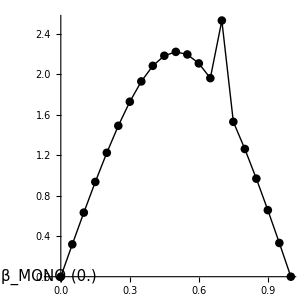

#### closest to TRIG, closest to CUBE

```mathematica
OutputFor[Tmat,TRIG]
OutputFor[Tmat,CUBE]
```

#### Reconstruct the problematic map.

```mathematica
TmatTRIG=Closest[Tmat,TRIG];
TmatCUBE=Closest[Tmat,CUBE];
Tmatx=0.3TmatTRIG+0.7TmatCUBE;
MatrixForm[TmatTRIG]
MatrixForm[TmatCUBE]
MatrixForm[Tmatx]
```

#### This fails to find the global minimum (β = 2.53 vs β = 1.76):

```mathematica
OutputFor[Tmatx,MONO]
```

#### CORRECT MINIMUM (β = 1.76): Upper left blue patch and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.3π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### INCORRECT MINIMUM (β = 2.53): Blue patch (green point) on the equator and its antipode region:

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### More detailed plot of the contours (hover the mouse over any contour)

```mathematica
ContourPlot[Alpha[Tmatx,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},Contours->Range[2,8],PlotPoints->20,ContourShading->None,AspectRatio->Automatic,ImageSize->700]
```

## The rest of the “fail” examples occurred when we were using a 2D search over MONO. These were all successful when we switched to the 3D search.

## 2D Search for the closest MONO map to Tmat Make sure you Clear[GetTempAndθ0σ0ϕ0] and then re-run ES_FindSymGroups.nb when you are done, so that GetTempAndθ0σ0ϕ0 is re-set to the 3D search.

## Example 1: Brown map, 2D search with θ_max = π

```mathematica
Tmat = TmatBrownTypo;
```

#### The problematic point is the closest MONO to closestMONO (dt = 0.5). By definition, the closest MONO to closestMONO should have β = 0, but it does not. This impacts the trajectory from MONO to ORTH as well.

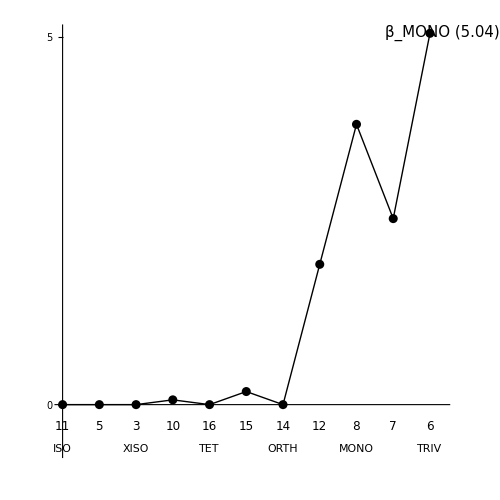

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π;
dphi=dtheta;
```

#### 2D search with θ_max = π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Closest MONO map to the input TRIV map (β = 5.04: this is correct):

```mathematica
OutputFor[Tmat,MONO]
```

#### CORRECT MINIMUM (β = 5.04): Upper left blue patch (green point) and its antipode region:

```mathematica
(* Flocal[0.5π,0.75π,dtheta,dphi,Tmat]
ArcSin[%[[1]]/NormMatrix[Tmat]]/Degree
Flocal[1.5π,0.3π,dtheta,dphi,Tmat]
ArcSin[%[[1]]/NormMatrix[Tmat]]/Degree *)
```

#### LOCAL MINIMUM (β = 5.21): Central blue patch and its antipode region:

```mathematica
(* Flocal[π,0.5π,dtheta,dphi,Tmat]
ArcSin[%[[1]]/NormMatrix[Tmat]]/Degree
Flocal[0.,0.5π,dtheta,dphi,Tmat]
ArcSin[%[[1]]/NormMatrix[Tmat]]/Degree *)
```

#### LOCAL MINIMUM (β = 5.16): Lower left blue patch and its antipode region:

```mathematica
(* Flocal[0.4 π,0.2π,dtheta,dphi,Tmat]
ArcSin[%[[1]]/NormMatrix[Tmat]]/Degree
Flocal[1.4π,0.8π,dtheta,dphi,Tmat]
ArcSin[%[[1]]/NormMatrix[Tmat]]/Degree *)
```

#### The full search finds the right minimum (as before):

```mathematica
(* Flocal[π,0.5π,π,0.5π,Tmat]
ArcSin[%[[1]]/NormMatrix[Tmat]]/Degree *)
```

#### Problematic map.

```mathematica
TmatMONO=Closest[Tmat,MONO];
MatrixForm[TmatMONO]
```

#### This fails to find the global minimum (β = 3.81 vs β =0):

```mathematica
OutputFor[TmatMONO,MONO]
```

```mathematica
βT[TmatMONO,MONO]/Degree
```

#### CORRECT MINIMUM (β ~ 0): Upper left blue patch and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,TmatMONO]
ArcSin[%[[1]]/NormMatrix[TmatMONO]]/Degree
(* Flocal[1.5π,0.3π,dtheta,dphi,TmatMONO]
ArcSin[%[[1]]/NormMatrix[TmatMONO]]/Degree *)
```

#### INCORRECT MINIMUM (β = 3.81): Central blue patch and its antipode region:

```mathematica
Flocal[π,0.5π,dtheta,dphi,TmatMONO]
ArcSin[%[[1]]/NormMatrix[TmatMONO]]/Degree
(* Flocal[0.,0.5π,dtheta,dphi,TmatMONO]
ArcSin[%[[1]]/NormMatrix[TmatMONO]]/Degree *)
```

#### LOCAL MINIMUM (β = 3.81): Lower left blue patch (green dot) and its antipode region:

```mathematica
Flocal[0.4 π,0.2π,dtheta,dphi,TmatMONO]
ArcSin[%[[1]]/NormMatrix[TmatMONO]]/Degree
(* Flocal[1.4π,0.8π,dtheta,dphi,TmatMONO]
ArcSin[%[[1]]/NormMatrix[TmatMONO]]/Degree *)
```

#### By extending the θ search range slightly, the 2D search finds the correct minimum (β ~ 0):

```mathematica
fac=1.15; (* NMinimize fails *)
fac=1.2; (* NMinimize works *)
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤fac π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
OutputFor[TmatMONO,MONO]
```

```mathematica
βT[TmatMONO,MONO]/Degree
```

#### The 3D search finds the correct minimum (β ~ 0):

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
OutputFor[TmatMONO,MONO]
```

## Example 2: Brown map, 2D search with θ_max = 2π

```mathematica
Tmat = TmatBrownTypo;
```

#### The problematic point is between TET and XISO (dt =0.2):

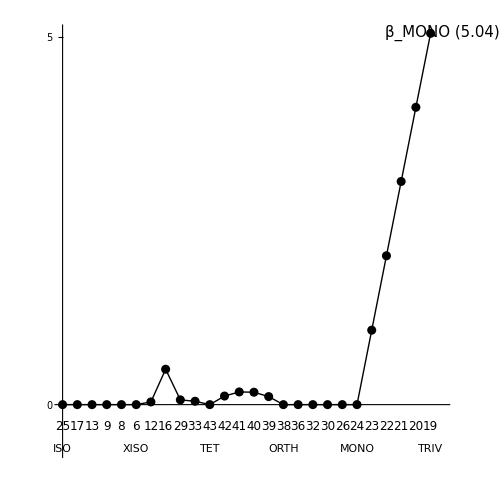

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π; dphi=dtheta;
```

#### 2D search with θ_max = 2π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤2π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Check the starting value of TRIV (β = 5.04)

```mathematica
(* OutputFor[Tmat,MONO] *)
```

#### closest to TET, closest to XISO

```mathematica
OutputFor[Tmat,TET]
OutputFor[Tmat,XISO]
```

#### Reconstruct the problematic map.

```mathematica
TmatTET=Closest[Tmat,TET];
TmatXISO=Closest[Tmat,XISO];
Tmatx=0.4TmatTET+0.6TmatXISO;
MatrixForm[TmatTET]
MatrixForm[TmatXISO]
MatrixForm[Tmatx]
```

#### This fails to find the global minimum (β = 0.48 vs β =0.06):

```mathematica
OutputFor[Tmatx,MONO]
```

#### CORRECT MINIMUM (β = 0.06): blue patch near θ = 0

```mathematica
Flocal[π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[0,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### INCORRECT MINIMUM (β = 0.481): blue path near θ = pi/2

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### LOCAL MINIMUM (β = 0.484): blue patch near poles

```mathematica
Flocal[0.7π,0.9π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.7π,0.1π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### Change the θ search range to π, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### Change to a 3D search, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
```

```mathematica
OutputFor[Tmatx,MONO]
```

## Example 3: Igel map, 2D search with θ_max = 2π

```mathematica
Tmat = TmatIgel;
```

#### The problematic point is between TRIV and MONO (dt = 0.2):

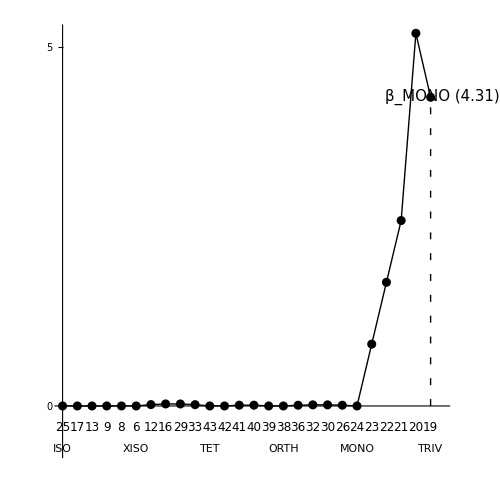

```mathematica
dtheta = 0.1π;
dphi=dtheta;
```

#### 2D search with θ_max = 2π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤2π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Closest MONO map to the input TRIV map:

```mathematica
OutputFor[Tmat,MONO]
```

#### Reconstruct the problematic map.

```mathematica
TmatMONO=Closest[Tmat,MONO];
Tmatx=0.8Tmat+0.2TmatMONO;
MatrixForm[Tmatx]
```

#### This fails to find the global minimum (β = 5.20 vs β =3.45):

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### The green dot in the contour plot turns out to be a local minimum, as we see next.

#### CORRECT MINIMUM (β = 3.45): blue patch at the center and its antipode region:

```mathematica
Flocal[π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[0,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### INCORRECT MINIMUM (β = 2.138): blue patch (with green dot) to the upper left of center:

```mathematica
Flocal[0.8 π,0.6π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
```

#### Change the search range back to π, and it works:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### Change to a 3D search, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
```

```mathematica
OutputFor[Tmatx,MONO]
```

## Example 4: TmatMar17 map, 2D search with θ_max = π

```mathematica
Tmat = TmatMar17;
```

#### The problematic point is between ORTH and TET (dt =0.2, θ_max = π):

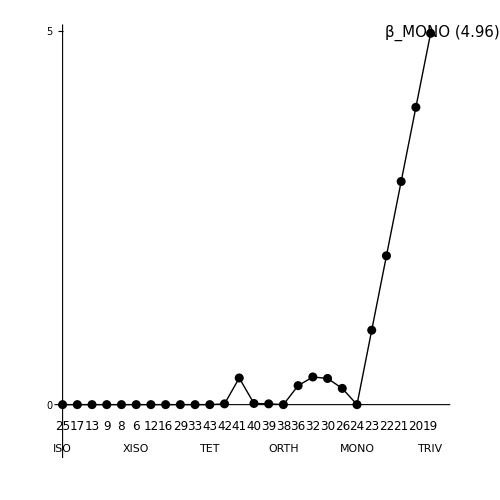

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π; dphi=dtheta;
```

#### 2D search with θ_max = π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Check the starting value of TRIV (β_MONO= 4.96)

```mathematica
(* OutputFor[Tmat,MONO] *)
```

#### closest to ORTH, closest to TET

```mathematica
OutputFor[Tmat,TET]
OutputFor[Tmat,ORTH]
```

#### Reconstruct the problematic map.

```mathematica
TmatTET=Closest[Tmat,TET];
TmatORTH=Closest[Tmat,ORTH];
Tmatx=0.6TmatTET+0.4TmatORTH;
MatrixForm[TmatTET]
MatrixForm[TmatORTH]
MatrixForm[Tmatx]
```

#### This fails to find the global minimum (it finds β = 0.356^o, but the minimum is β = 0.015^o):

```mathematica
OutputFor[Tmatx,MONO]
```

#### LOCAL MINIMUM (β = 0.36): blue sausage near θ = 2π

```mathematica
Flocal[1.95π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[0.95 π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### INCORRECT MINIMUM (β = 0.36): blue sausage near θ = π/2

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### CORRECT MINIMUM (β = 0.197): blue isolated patch

```mathematica
Flocal[0.4π,0.2π,dtheta,dphi,Tmatx]
```

#### Change the θ search range to 2π, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤2π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### Change to a 3D search, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
```

```mathematica
OutputFor[Tmatx,MONO]
```